```mathematica
(*  AQC // Matthew Berntson //  4/12/16 *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
sz={{1,0},{0,-1}};
sx={{0,1},{1,0}};
ID=IdentityMatrix[2];
```

### Example for the LockBox problem, using an Ising Hamiltonian derived from a binary programming formulation. For the Ising Hamiltonian, the spin couplings J_{ij} = 2*A*Sum_{j=1}^m S_ji S_jl for i!=j, and J_{ii} = A*Sum_{j=1}^m S_ji^2 for i==j . The magnetic field parameters h_{i} = B*c_i + 2*A*Sum_{j=1}^m b_j S_ji.

```mathematica
(* The data for the matrices of cost (c), coupling (S), and constraint (b) are as follows *)
```

```mathematica
(* Number of binary variables *)
```

```mathematica
Num=16;
```

```mathematica
(* Number of constraints *)
```

```mathematica
m=4;
```

```mathematica
(* constants A and B are dictated by Num, s.t. A/B~>N *)
```

```mathematica
A=Num;
B=1;
```

```mathematica
(* c is the cost vector (want to minimize so use -1) *)
```

```mathematica
c = -1*{28,84,112,112,
60,20,50,50,
96,60,24,60,
64,40,40,16};
```

```mathematica
(* S is the array of constraints (lhs) for the system of eqns *)
```

```mathematica
S ={{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0},	{0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}};
```

```mathematica
(* b is the array of constraints (rhs) *)
```

```mathematica
b ={1,1,1,1};
```

```mathematica
(* Now calculate coupling and field parameters *)
```

```mathematica
(* Field Parameters *)
```

```mathematica
h={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
For[i=1,i<Num+1,i++,h[[i]]=B*c[[i]]+2*A*Sum[b[[j]]*S[[j]][[i]],{j,m}]]
```

```mathematica
MatrixForm[h]
```

(4
-52
-80
-80
-28
12
-18
-18
-64
-28
8
-28
-32
-8
-8
16)

```mathematica
(* Coupling Terms *)
```

```mathematica
J={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
(* Calculate all elements using the i≠l formula *)
```

```mathematica
For[l=1,l<Num+1,l++,For[i=l,i<Num+1,i++,J[[l]][[i]]=2*A*Sum[S[[j]][[i]]*S[[j]][[l]],{j,m}]]]
```

```mathematica
MatrixForm[J]
```

(32 | 32 | 32 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 32 | 32 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 32 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 32 | 32 | 32 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 32 | 32 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 32 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 32 | 32 | 32 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 32 | 32 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 32 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 32 | 32 | 32
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 32 | 32
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32 | 32
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32)

```mathematica
(* Replace diagonal elements with i==j formula *)
```

```mathematica
For[i=1,i<Num+1,i++,J[[i]][[i]]=A*Sum[S[[j]][[i]]*S[[j]][[i]],{j,m}]]
```

```mathematica
MatrixForm[J]
```

(16 | 32 | 32 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16 | 32 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 16 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 16 | 32 | 32 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 16 | 32 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 16 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 32 | 32 | 32 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 32 | 32 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 32 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 32 | 32 | 32
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 32 | 32
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 32
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16)

```mathematica
2^16
```

65536

```mathematica
(* For this problem, we need a 2^Num by 2^Num matrix to represent the problem Hamiltonian, therefore I am moving to the Python code to attempt to build the algorithm to find this matrix without hardcoding *)
```

```mathematica
(* Everything below this line needs functionality to perform recursive kronecker products.  Also, I am not sure if Mathematica can operate on matrices of the required size. *)
```

```mathematica
(* Hard code the spins *)
```

```mathematica
(* Note that the spins for the diagonal coupling terms are z_{i}^2 *)
```

```mathematica
z1=KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,ID]]]];
```

```mathematica
z2=KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,ID]]]];
```

```mathematica
z3=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,ID]]]];
```

```mathematica
z4=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,ID]]]];
```

```mathematica
z5=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,sz]]]];
```

```mathematica
z12=KroneckerProduct[sz,KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,ID]]]];
```

```mathematica
z13=KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,ID]]]];
```

```mathematica
z14=KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,ID]]]];
```

```mathematica
z15=KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,sz]]]];
```

```mathematica
z23=KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[sz,KroneckerProduct[ID,ID]]]];
```

```mathematica
z24=KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[sz,ID]]]];
```

```mathematica
z25=KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,KroneckerProduct[ID,sz]]]];;
```

```mathematica
z34=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[sz,ID]]]];
```

```mathematica
z35=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,KroneckerProduct[ID,sz]]]];;
```

```mathematica
z45=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sz,sz]]]];
```

```mathematica
(* Add field terms to problem hamiltonian *)
```

```mathematica
hp=-1*(h[[1]]z1+h[[2]]z2+h[[3]]z3+h[[4]]z4+h[[5]]z5);
```

```mathematica
(* Add coupling terms to problem hamiltonian *)
```

```mathematica
hp+=-1*(J[[1]][[1]] z1^2+J[[1]][[2]] z12+J[[1]][[3]] z13+J[[1]][[4]] z14+J[[1]][[5]]z15+J[[2]][[2]] z2^2+J[[2]][[3]]z23+J[[2]][[4]]z24+J[[2]][[5]]z25+J[[3]][[3]] z3^2+J[[3]][[4]]z34+J[[3]][[5]]z35+J[[4]][[4]] z4^2+J[[4]][[5]]z45+J[[5]][[5]] z5^2);
```

```mathematica
x12=KroneckerProduct[sx,KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[ID,ID]]]];;
```

```mathematica
x13=KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[ID,ID]]]];;
```

```mathematica
x14=KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sx,ID]]]];;
```

```mathematica
x15=KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,sx]]]];;
```

```mathematica
x23=KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[sx,KroneckerProduct[ID,ID]]]];
```

```mathematica
x24=KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[sx,ID]]]];
```

```mathematica
x25=KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[ID,KroneckerProduct[ID,sx]]]];
```

```mathematica
x34=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[sx,ID]]]];
```

```mathematica
x35=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sx,KroneckerProduct[ID,sx]]]];
```

```mathematica
x45=KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[ID,KroneckerProduct[sx,sx]]]];
```

```mathematica
hinit=-1*(x12+x13+x14+x15+x23+x24+x25+x34+x35+x45) ;(* placeholder initial Hamiltonian, something simpler would be more practical *)
```

```mathematica
htot[s_]:=s hp+(1-s) hinit
```

```mathematica
evals=Eigenvalues[htot[s]];
```

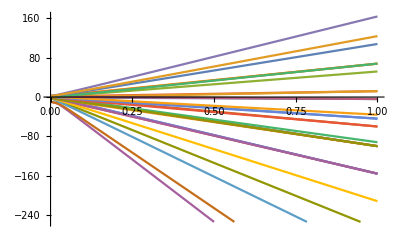

```mathematica
Plot[evals,{s,0,1}]
```

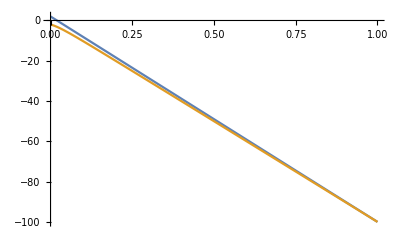

```mathematica
Plot[{evals[[1]],evals[[2]]},{s,0,1}]
```

```mathematica
nppgap[s_]:=evals[[1]]-evals[[2]]
```

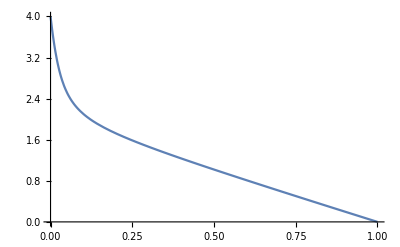

```mathematica
Plot[nppgap[s],{s,0,1}]
```